# PS 17 — Rania 4.8.2025

## Section 39

= vs. := (delayed)
x-> vs. x :>

```mathematica
(*39.1 Replace x in {x,x+1,x+2,x^2} by the same random integer up to 100. *)
{x, x+1, x+2, x^2}/.x-> RandomInteger[100]
```

{43,44,45,1849}

```mathematica
(*39.2 Replace each x in {x,x+1,x+2,x^2} by a separately chosen random integer up to 100.*)
```

```mathematica
{x, x+1, x+2, x^2}/.x:>RandomInteger[100]
```

{42,34,93,64}

## Section 40

```mathematica
(*40.1 Define a function f that computes the square of its argument*)
```

```mathematica
f[x_]:= x*x
{f[2],f[4], f[6]}
```

{4,16,36}

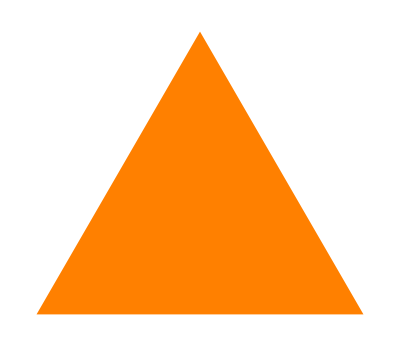
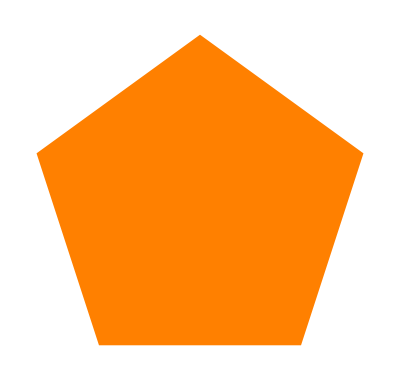
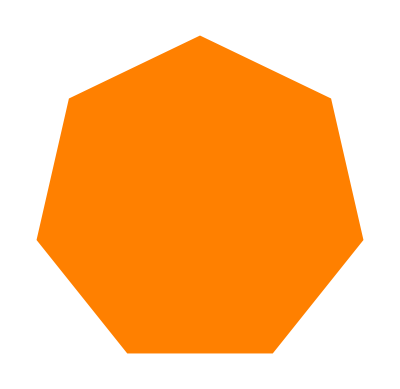

```mathematica
(*40.2 Define a function poly that takes an integer,and makes a picture of an orange regular polygon with that number of sides*)
poly[n_]:=Graphics[Style[RegularPolygon[n], Orange]]
{poly[3],poly[5], poly[7]}
```

```mathematica
(*40.3 Define a function f that takes a list of two elements and puts them in reverse order*)
f[{x_, y_}] := {y, x}
f[{1,2}]
```

{2,1}

```mathematica
(*40.4 Create a function f that takes two arguments and gives the result of multiplying them and dividing by their sum.*)
f[{x_,y_}] := (x*y)/(x+y)
f[{4,5}]
```

20/9

```mathematica
(*40.5 Define a function f that takes a list of two elements and returns a list of their sum,difference and ratio *)
f[{x_, y_}]:= {x+y, x-y, x/y}
f[{3,4}]
```

{7,-1,3/4}

```mathematica
(*40.6 Define a function evenodd that gives Black if its argument is even and White otherwise,but gives Red if its argument is 0 *)
evenodd[x_] := If[x==0,Red,If[EvenQ[x]==True,Black, White]]
{evenodd[0],evenodd[1],evenodd[2]} (*lol the egyptian flag colors*)
```

{RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[0]}

```mathematica
(*40.7 Define a function f of three arguments where the second two arguments are added if the first argument is 1,multiplied if it’s 2 and raised to a power if it’s 3*)
f[{x_,y_, z_}]:= If[x==1, y+z, If[x==2, y*z,If[x==3, y^z, "First Argument is not 1, 2, 3"]]]
{f[{1,2,3}], f[{2,2,3}],f[{3,2,3}]}
```

{5,6,8}

```mathematica
(*40.8Define a Fibonacci function f with f[0] and f[1] both being 1,and f[n] for integer n being the sum of f[n-1] and f[n-2]*)
f[x_]:= If[x!=0 && x!= 1,f[x-1]+f[x-2],1]
f/@ Range[5]
```

{1,2,3,5,8}

```mathematica
(*40.9 Create a function animal that takes a string,and gives a picture of an animal with that name.*)
animal[x_]:=Interpreter["Animal"][x][EntityProperty["TaxonomicSpecies","Image"]]
animal[#]&/@{"horse","cat", "camel"}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*40.10 Define a function nearwords that takes a string and an integer n,and gives the n words in WordList[] that are nearest to a given string.*)
```

```mathematica
nearwords[x_,n_]:=Nearest[WordList[],x,n+1]
nearwords["hello",2]
nearwords["brian",9]
nearwords["waves", 22]
```

{hello,cello}

{bran,aria,avian,bairn,ban,barman,bean,bias,bin}

{eaves,wages,wave,waver,aver,cave,elves,fives,gavel,have,haven,heaves,hives,lave,mates,maven,names,nave,navel,pave,paved,rates}